## O(4) model high temperature limit Nv=3

```mathematica
Series[1/2+1/(Exp[(√(1+mpibar2[rho]))/Ttilde]-1),{Ttilde,∞,2}]
```

General::ivar: 635800399/8000 不是一个有效的变量.

Series[1/2+1/(-1+ⅇ^((8000 √(1+mpibar2[rho]))/635800399)),{635800399/8000,∞,2}]

```mathematica
dtVbar[rho_]:=-3Vbar[rho]+rho lam1bar[rho]+1/(6 π^2)((N1-1)/(1+lam1bar[rho])+1/(1+(lam1bar[rho]+2rho lam2bar[rho])));
dtlam1[rho_]:=D[dtVbar[rho],rho]
dtlam2[rho_]:=D[dtlam1[rho],rho]
dtlam3[rho_]:=D[dtlam2[rho],rho]
```

```mathematica
rep={lam1bar[0]->lam1bar,lam1bar'[0]->lam2bar,lam1bar''[0]->lam3bar,Derivative[3][lam1bar][0]->0,lam2bar[0]->lam2bar,lam2bar'[0]->lam3bar,lam2bar''[0]->0,Vbar'[0]->lam1bar,Vbar''[0]->lam2bar,Derivative[3][Vbar][0]->lam3bar};
```

```mathematica
dtlam1exp=dtlam1[rho]/.{rho->0}/.rep
dtlam2exp=dtlam2[rho]/.{rho->0}/.rep
dtlam3exp=dtlam3[rho]/.{rho->0}/.rep
```

-2 lam1bar+(-(3 lam2bar)/(1+lam1bar)^2-(lam2bar (-1+N1))/(1+lam1bar)^2)/(6 π^2)

-lam2bar+((18 lam2bar^2)/(1+lam1bar)^3-(5 lam3bar)/(1+lam1bar)^2+(2 lam2bar^2 (-1+N1))/(1+lam1bar)^3-(lam3bar (-1+N1))/(1+lam1bar)^2)/(6 π^2)

(-(162 lam2bar^3)/(1+lam1bar)^4+(90 lam2bar lam3bar)/(1+lam1bar)^3-(6 lam2bar^3 (-1+N1))/(1+lam1bar)^4+(6 lam2bar lam3bar (-1+N1))/(1+lam1bar)^3)/(6 π^2)

```mathematica
dtlam1fun[N1_,lam1bar_,lam2bar_,lam3bar_]:=-2 lam1bar+(-(3 lam2bar)/(1+lam1bar)^2-(lam2bar (-1+N1))/(1+lam1bar)^2)/(6 π^2);
dtlam2fun[N1_,lam1bar_,lam2bar_,lam3bar_]:=-lam2bar+((18 lam2bar^2)/(1+lam1bar)^3-(5 lam3bar)/(1+lam1bar)^2+(2 lam2bar^2 (-1+N1))/(1+lam1bar)^3-(lam3bar (-1+N1))/(1+lam1bar)^2)/(6 π^2);
dtlam3fun[N1_,lam1bar_,lam2bar_,lam3bar_]:=(-(162 lam2bar^3)/(1+lam1bar)^4+(90 lam2bar lam3bar)/(1+lam1bar)^3-(6 lam2bar^3 (-1+N1))/(1+lam1bar)^4+(6 lam2bar lam3bar (-1+N1))/(1+lam1bar)^3)/(6 π^2);
```

## Fix point 1

```mathematica
n=4;
FindRoot[{dtlam1fun[n,lam1bar,lam2bar,0]==0,dtlam2fun[n,lam1bar,lam2bar,0]==0},{{lam1bar,-1/9},{lam2bar,(128 π^2)/729}}]
```

{lam1bar→-0.111111,lam2bar→1.73293}

```mathematica
matrix={D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
Eigenvalues[matrix/.{lam1bar->0,lam2bar->0,lam3bar->0}]
```

{-2,-1,0}

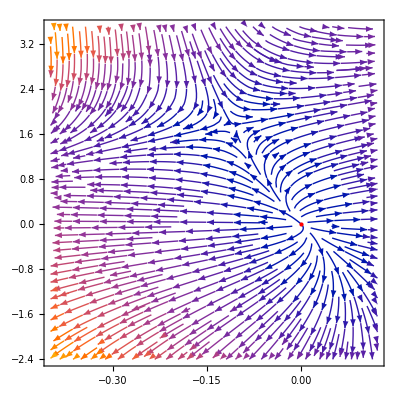

```mathematica
myStreamPlot[{-dtlam1fun[n,lam1bar,lam2bar,0.],-dtlam2fun[n,lam1bar,lam2bar,0.]},{lam1bar,-0.4(*-13/41*),5/41},{lam2bar,-2.4,3.5},StreamPoints->{500,0.005},Epilog->{Red,PointSize[Large],Point[{0,0}]}]
```

## Fix point 2

```mathematica
n=4;
Solve[{-dtlam1fun[n,lam1bar,lam2bar,lam3bar]==0,-dtlam2fun[n,lam1bar,lam2bar,lam3bar]==0,-dtlam3fun[n,lam1bar,lam2bar,lam3bar]==0},{lam1bar,lam2bar,lam3bar}]
```

{{lam1bar→-9/41,lam2bar→(18432 π^2)/68921,lam3bar→(17694720 π^4)/115856201},{lam1bar→0,lam2bar→0,lam3bar→0}}

```mathematica
matrix={D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
eign=Eigenvalues[matrix/.{lam1bar->-9/41,lam2bar->(18432 π^2)/68921,lam3bar->(17694720 π^4)/115856201}]//N
```

{12.9187,-1.50401,1.33533}

```mathematica
eign^-1//N
```

{0.0774073,-0.664888,0.748878}

```mathematica
Options[myStreamPlot]=Options[StreamPlot];
myStreamPlot[f_,{x_,x0_,x1_},{y_,y0_,y1_},opts:OptionsPattern[]]:=With[{a=OptionValue[AspectRatio]},Show[StreamPlot[{1/(x1-x0),a/(y1-y0)} (f/. {x->x0+u (x1-x0),y->y0+v/a (y1-y0)}),{u,0,1},{v,0,a},opts]/. Arrow[pts_]:>Arrow[({x0,y0}+{x1-x0,(y1-y0)/a} #)&/@pts],PlotRange->{{x0,x1},{y0,y1}}]]
```

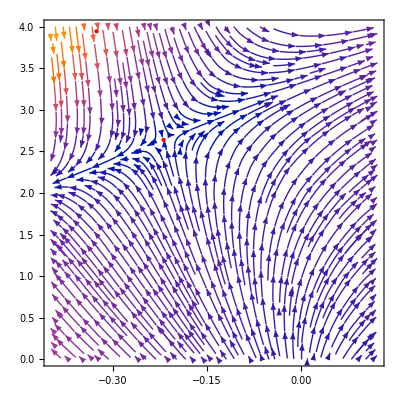

```mathematica
myStreamPlot[{-dtlam1fun[n,lam1bar,lam2bar,(17694720 π^4)/115856201],-dtlam2fun[n,lam1bar,lam2bar,(17694720 π^4)/115856201]},{lam1bar,-0.4(*-13/41*),5/41},{lam2bar,0,4},StreamPoints->{200,0.004},Epilog->{Red,PointSize[Large],Point[{-9/41,(18432 π^2)/68921}],Point[{-0.326531,3.94411}]}]
```

```mathematica
-400^2/700^2//N
```

-0.326531

```mathematica
25*86.552723235/700
```

3.09117

```mathematica
-9/41//N
```

-0.219512

```mathematica
(18432 π^2)/68921//N
```

2.63949

```mathematica
(17694720 π^4)/115856201//N
```

14.8773

```mathematica
14.8773/700^2
```

0.0000303618